# Fourier Series Solution for Stationary Toxin Field, Periodic BC.

## Initializing

```mathematica
(* Model Parameters *)
s[x_]:= Cos[x*2*Pi] + 1.5
L = 1; (*Domain size in x*)
l = Integrate[1/s[x],{x,0,L}]; (*Domain size in y*)
F = 1;
(* Fourier Parameters *)
FourierN = 100 ; (*Fourier series pieces*)
R[n_]:= Sqrt[F^2 - (2*Pi*n/l)^2] (*Char root piece*)
```

## Fourier Coefficients for Mpm(y,0), dMydtpm(y,0)

### Find x[y] and s[y] via inverse function

```mathematica
Integrate[1/(Cos[2*Pi*x]+3/2),x]//Simplify
```

(2 ArcTan[Tan[π x]/(√5)])/(√5 π)

```mathematica
InverseFunction[ConditionalExpression[(2 ArcTan[Tan[π #]/(√5)])/(√5 π), 0<#<1/2]&][y]
```

ConditionalExpression[ArcTan[√5 Tan[1/2 √5 π y]]/π,0<y<1/(√5)]

```mathematica
yFromX[x_] := NIntegrate[1/(Cos[2*Pi*x1]+3/2),{x1,0,x}]
xFromY[y_]:=ArcTan[√5 Tan[1/2 √5 π y]]/π(* Somewhat problematic *)
(*sFromY[y_]:= s[xFromY[y]]*)
sFromY[y_]:=3/2+Cos[2 ArcTan[√5 Tan[1/2 √5 π y]]]
```

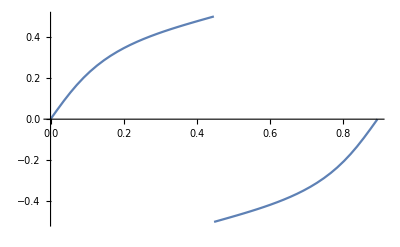

```mathematica
Plot[xFromY[y],{y,0,l}]
```

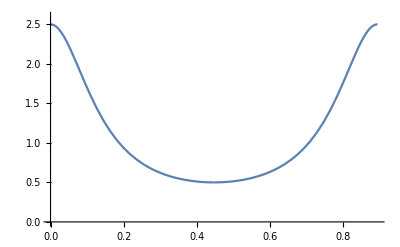

```mathematica
Plot[sFromY[y],{y,0,l}, PlotRange->{0,2.6}]
```

### Find Mp (y, 0) and Mm (y, 0)

```mathematica
(*MypInitial[y_]:= sFromY[y] * Pp[y,0] *)
MypInitial[y_]:= 1/2*(3/2+Cos[2 ArcTan[√5 Tan[1/2 √5 π y]]])
(*MymInitial[y_]:= -sFromY[y] * Pm[y,0] *)
MymInitial[y_]:= -1/2*(3/2+Cos[2 ArcTan[√5 Tan[1/2 √5 π y]]])
```

```mathematica
NIntegrate[MymInitial[y]*Exp[-ⅈ*2*Pi*0*y/l]/l,{y,0,l}]
```

-0.559017

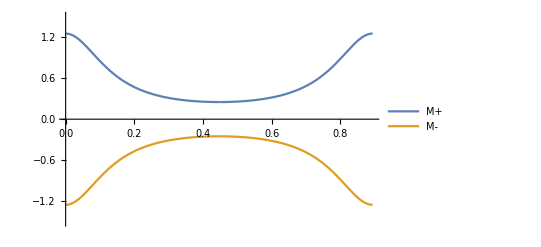

```mathematica
Plot[{MypInitial[y],MymInitial[y]},{y,0,l},PlotRange->{-1.5,1.5}, PlotLegends->{"M+","M-"}]
```

### Check if Mp(y,0) Mm(y,0) is right

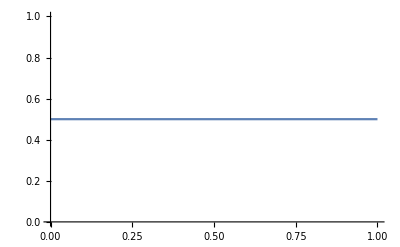

```mathematica
Xcoord = Subdivide[0,L,500];
Ycoord = yFromX /@ Xcoord;
MCheckTable = MymInitial /@ Ycoord;
sTable = -s /@ Xcoord;
CheckTable = MCheckTable/sTable;
Plt = ListLinePlot[Table[{Xcoord[[i]] ,CheckTable[[i]]},{i,1,Length[Xcoord]}],PlotRange->{0,1}];
Show[Plt]
```

### Find dMpdt (y, 0) and dMmdt (y, 0)

```mathematica
(* dMydtpInitial[y] *)
-D[MypInitial[y],y] - F*(MymInitial[y] + MypInitial[y])//Simplify
```

(5 π Sin[2 ArcTan[√5 Tan[1/2 √5 π y]]])/(6-4 Cos[√5 π y])

```mathematica
(* dMydtmInitial[y] *)
+D[MymInitial[y],y] - F*(MypInitial[y] + MymInitial[y])//Simplify
```

(5 π Sin[2 ArcTan[√5 Tan[1/2 √5 π y]]])/(6-4 Cos[√5 π y])

```mathematica
(* dMydtpInitial[y_]=-D[MypInitial[y],y] - F*(MymInitial[y] + MypInitial[y])//Simplify *)
dMydtpInitial[y_] := (5 π Sin[2 ArcTan[√5 Tan[1/2 √5 π y]]])/(6-4 Cos[√5 π y])
(* dMydtmInitial[y_]=+D[MymInitial[y],y] - F*(MypInitial[y] + MymInitial[y])//Simplify *)
dMydtmInitial[y_]:=(5 π Sin[2 ArcTan[√5 Tan[1/2 √5 π y]]])/(6-4 Cos[√5 π y])
```

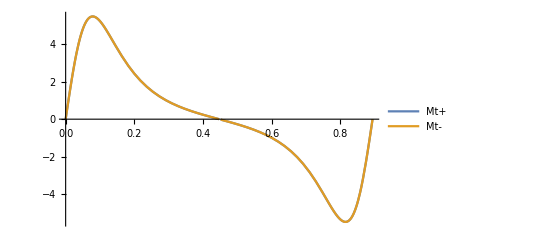

```mathematica
Plot[{dMydtmInitial[y],dMydtpInitial[y]},{y,0,l},PlotLegends->{"Mt+","Mt-" }]
```

### Find n - th Fourier Coefficients for Mp (y, 0), Mm (y, 0)

```mathematica
<<FourierSeries`
MpFourierTable =  Table[NIntegrate[MypInitial[y]*Exp[-ⅈ*2*Pi*n*y/l]/(l),{y,0,l}],{n,-FourierN, FourierN}];
MmFourierTable =  Table[NIntegrate[MymInitial[y]*Exp[-ⅈ*2*Pi*n*y/l]/(l),{y,0,l}],{n,-FourierN, FourierN}];
```

```mathematica
UP[n_]:=MpFourierTable[[n + FourierN + 1]]
UM[n_]:=MmFourierTable[[n + FourierN + 1]]
```

```mathematica
NIntegrate[MypInitial[y]*Exp[-ⅈ*2*Pi*0*y/l]/l,{y,0,l}]
```

0.559017

```mathematica
NIntegrate[MymInitial[y]*Exp[-ⅈ*2*Pi*0*y/l]/l,{y,0,l}]
```

-0.559017

```mathematica
(*M+ - M- = sP+ - (-sP-) = s (P+ + P-)*)
```

### Find n - th Fourier Coefficients for dMp/dt (y, 0),dMm/dt (y, 0)

```mathematica
dMdtpFourierTable =  Table[NIntegrate[dMydtpInitial[y]*Exp[-ⅈ*2*Pi*n*y/l]/(l),{y,0,l}],{n,-FourierN, FourierN}];
dMdtmFourierTable =  Table[NIntegrate[dMydtmInitial[y]*Exp[-ⅈ*2*Pi*n*y/l]/(l),{y,0,l}],{n,-FourierN, FourierN}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.89437761850858729907679791834573812536746117984876036643981933594}. NIntegrate obtained 2.75818×10^-12 and 1.59911×10^-12 for the integral and error estimates.

```mathematica
WP[n_]:=dMdtpFourierTable[[n + FourierN + 1]]
WM[n_]:=dMdtmFourierTable[[n + FourierN + 1]]
```

## Aplus, Aminus, Bplus, Bminus ,Cplus, Cminus

```mathematica
AP[n_]:=((F + R[n])*UP[n]+ WP[n])/(2*R[n])
AM[n_]:=((F + R[n])*UM[n] + WM[n])/(2*R[n])
BP[n_]:=((-F+R[n])*UP[n]- WP[n])/(2*R[n])
BM[n_]:=((-F+R[n])*UM[n]- WM[n])/(2*R[n])
```

```mathematica
CP[n_,t_]:=AP[n]*Exp[(-F+R[n])*t] + BP[n]*Exp[(-F-R[n])*t]
CM[n_,t_]:=AM[n]*Exp[(-F+R[n])*t] + BM[n]*Exp[(-F-R[n])*t]
```

```mathematica
MEql[y_]:= Re[(AP[0]-AM[0])/ sFromY[y]]
```

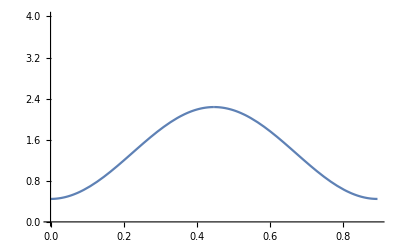

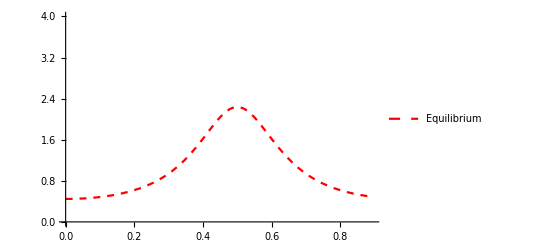

```mathematica
Plot[MEql[y],{y,0,l}, PlotRange->{0, 4}]
Plot[1/s[x]/l,{x,0,l},PlotRange->{0,4},PlotStyle->{Red,Dashed},PlotLegends->{"Equilibrium"}]
```

```mathematica
NIntegrate[MEql[y],{y,0,l}]
```

1.2

## Now calculate the M(y,t)

```mathematica
Mtx = {{1,1},{-FF + RR, -FF - RR}};
Inverse[Mtx]//Simplify//MatrixForm
```

((FF+RR)/(2 RR) | 1/(2 RR)
(-FF+RR)/(2 RR) | -1/(2 RR))

```mathematica
NIntegrate[MypInitial[y]/l,{y,0,l}]
```

0.559017

```mathematica
-F+R[0]
```

0.

```mathematica
AP[0]+BP[0]
```

0.559017

```mathematica
AM[0]+BM[0]
```

-0.559017

```mathematica
Limit[Exp[(-F-R[0])*t],t->Infinity]
```

0.

```mathematica
Exp[(-F+R[0])*100]
```

1.

```mathematica
CP[0,100]
```

0.838525

```mathematica
AP[0]*Exp[(-F+R[0])*100]
```

0.838525

```mathematica
AP[0]
```

0.838525

```mathematica
AM[0]
```

-0.838525

```mathematica
Sum[CP[n,100]*Exp[2*Pi*ⅈ*n*0.5/l],{n,-FourierN, FourierN}]
```

0.559017+1.87118×10^-61 ⅈ

```mathematica
MpFSeries[y_,t_] := Re[Sum[CP[n,t]*Exp[2*Pi*ⅈ*n*y/l],{n,-FourierN, FourierN}] ]
MmFSeries[y_,t_] := Re[Sum[CM[n,t]*Exp[2*Pi*ⅈ*n*y/l],{n,-FourierN, FourierN}] ]
```

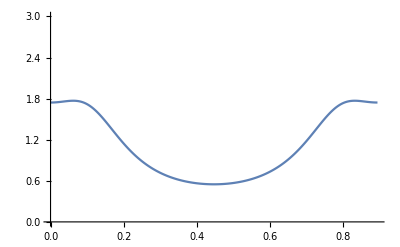

```mathematica
Xcoord = Subdivide[0,L,500];
(* Translated from evenly spaced x coordinate *) 
Ycoord = yFromX /@ Xcoord; 
MTableInit =Table[MpFSeries[y,0.1]-MmFSeries[y,0.1],{y,Ycoord}];
ListLinePlot[Table[{Ycoord[[i]] ,MTableInit[[i]]},{i,1,Length[Ycoord]}], PlotRange->{0,3}]
```

```mathematica
1/l (* Equilibrium M value *)
```

1.11803

### Calculate at 0, 0.01, 0.5, 10

```mathematica
MTable0 =Table[MpFSeries[y,0]-MmFSeries[y,0],{y,Ycoord}];
MTable0p1=Table[MpFSeries[y,0.1]-MmFSeries[y,0.1],{y,Ycoord}];
MTable0p5=Table[MpFSeries[y,0.5]-MmFSeries[y,0.5],{y,Ycoord}];
MTable1=Table[MpFSeries[y,1]-MmFSeries[y,1],{y,Ycoord}];
MTable10=Table[MpFSeries[y,10]-MmFSeries[y,10],{y,Ycoord}];
```

```mathematica
MTable0p15=Table[MpFSeries[y,0.15]-MmFSeries[y,0.15],{y,Ycoord}];
```

## Translate Back to P(x,t) and Save

### Translate from M(y,t) to P(x,t)

```mathematica
SigEquilibrium[x_]:= 1/s[x]/l
Xcoord = Subdivide[0,L,500];
sTable = s /@ Xcoord;
SigmaTable0 = MTable0/sTable;
SigmaTable0p1 = MTable0p1/sTable;
SigmaTable0p15 = MTable0p15/sTable;
SigmaTable0p5 = MTable0p5/sTable;
SigmaTable10 = MTable10/sTable;
SigmaTable1 = MTable1/sTable;
SigmaTableEquilibrium = SigEquilibrium /@ Xcoord;
```

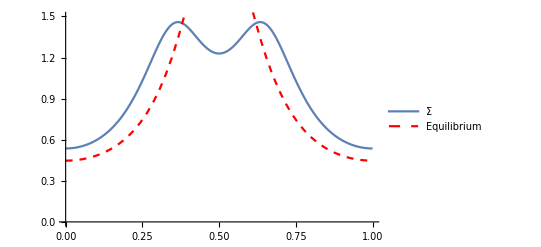

```mathematica
P1 = ListLinePlot[Table[{Xcoord[[i]] ,SigmaTable0p15[[i]]},{i,1,Length[Xcoord]}],PlotRange->{0, 1.5},PlotLegends->{"Σ"}];
P2 = Plot[1/s[x]/l,{x,0,1},PlotRange->{0,5},PlotStyle->{Red,Dashed},PlotLegends->{"Equilibrium"}];
Show[P1, P2]
```

```mathematica
Total[SigmaTable0p1]*(Xcoord[[2]]-Xcoord[[1]] )
```

1.00132

## Plot M+, M- values

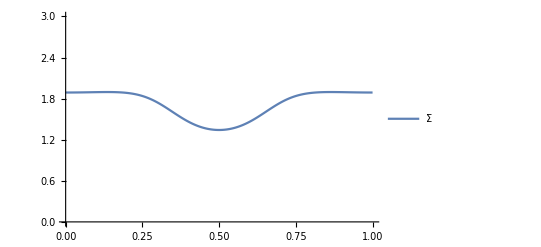

```mathematica
ListLinePlot[Table[{Xcoord[[i]] ,MTable1[[i]]},{i,1,Length[Xcoord]}],PlotRange->{0, 3},PlotLegends->{"Σ"}]
```

## Exporting

```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]]
```

D:\Research with Dr Rossi\Mathematica Scratch

```mathematica
datavert = Flatten/@Transpose[{Xcoord//N, SigmaTable0, SigmaTable0p1,SigmaTable0p15,SigmaTable0p5 , SigmaTable1 ,SigmaTable10}];
```

```mathematica
Export["D:\\Research with Dr Rossi\\Mathematica Scratch\\Fourier Series Sol Stationary Toxin Cosine.csv", datavert, TableHeadings-> {"xdata","Sig0","Sig0.1","Sig0.15","Sig0.5","Sig1","Sig10"}]
```

D:\Research with Dr Rossi\Mathematica Scratch\Fourier Series Sol Stationary Toxin Cosine.csv

## Fourier Coefficient Fix

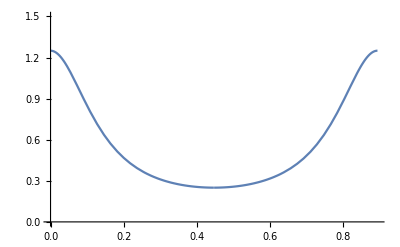

```mathematica
PMyp = Plot[MypInitial[y],{y,0,l},PlotRange->{0,1.5}]
```

```mathematica
FourierTable = Table[NFourierCoefficient[MypInitial[y],y,n, FourierParameters->{1, 2*Pi/l}],{n,-FourierN, FourierN}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {7.5204×10^-9}. NIntegrate obtained -2.00005×10^-12+1.02999×10^-18 ⅈ and 7.11109×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {7.5204×10^-9}. NIntegrate obtained 2.04003×10^-12+3.93023×10^-18 ⅈ and 8.35286×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {7.5204×10^-9}. NIntegrate obtained -2.08245×10^-12+2.56143×10^-18 ⅈ and 7.12453×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
TestCoeff[n_]:=FourierTable[[n + FourierN + 1]]
TestFunc[x_]:= Re[Sum[TestCoeff[n]*Exp[ⅈ*2*Pi*x*n/l],{n,-FourierN, FourierN}]]
```

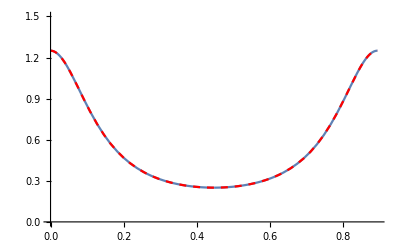

```mathematica
PMypF = Plot[TestFunc[x],{x,0,l},PlotRange->{0,1.5},PlotStyle->{Dashed,Red}];
Show[PMyp, PMypF]
```

```mathematica
FourierTabled = Table[NFourierCoefficient[dMydtpInitial[y],y,n, FourierParameters->{1, 2*Pi/l}],{n,-FourierN, FourierN}];
TestCoeffd[n_]:=FourierTabled[[n + FourierN + 1]]
TestFuncd[x_]:= Re[Sum[TestCoeffd[n]*Exp[ⅈ*2*Pi*x*n/l],{n,-FourierN, FourierN}]]
```

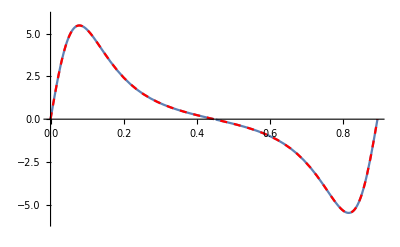

```mathematica
PMypd = Plot[dMydtpInitial[y],{y,0,l},PlotRange->{-6,6}];
PMypFd = Plot[TestFuncd[x],{x,0,l},PlotRange->{-6,6},PlotStyle->{Dashed,Red}];
Show[PMypd, PMypFd]
```

```mathematica
Mtx = {{1,1},{-FF + RR, -FF - RR}};
Inverse[Mtx]//Simplify
```

{{(FF+RR)/(2 RR),1/(2 RR)},{(-FF+RR)/(2 RR),-1/(2 RR)}}